### Distribution Problem, Sam Harris

#### Initial Setup and Genetic Algorithm

```mathematica
storeLocations = Append[#,RandomInteger[{1,30}]]&/@RandomReal[{0, 5}, {30, 2}];
n = 5;
supplyFromRegionals=ConstantArray[0, n-1];

Reproduction[parents_]:=
Module[{children},
children=ParallelMap[Mutation[#]&,parents]
];

ParentSelection[population_]:=
Module[{profits,parents},
profits=ParallelTable[
GetProfits[population[[i]]]
,{i,1,Length[population]}
];
TournamentSelection[population,profits,Length[population]]
];

Mutation[strategy_]:=
Module[{mutated, temp},
temp = strategy;
mutated = Table[
If[RandomReal[]<(1/(2*Length[strategy])),
temp[[i,1]] = MutateNumber[temp[[i, 1]]];
temp[[i, 2]] = MutateNumber[temp[[i, 2]]];
];
temp[[i]]
,{i,1,Length[temp]}
];
mutated
];

SetInitialSupply[strategy_] :=
Module[{value, result, initialVect},
value = Total[storeLocations[[All, 3]]];
supplyFromRegionals = SplitInteger[value, Length[strategy]-1]
];

SplitInteger[n_,k_]:=First[IntegerPartitions[n,{k},All,-1]];

UpdateSupply[strategy_] :=
Module[{closestArray, shortestDistToRegionals, distances},
shortestDistToRegionals = 
Table[
distances=Table[
EuclideanDistance[ storeLocations[[i, 1;;2]], strategy[[1+j]]]/(5-Exp[-(supplyFromRegionals[[j]])])
,{j, 1, Length[strategy]-1}
];
Ordering[distances, 1][[1]]
, {i, 1, Length[storeLocations]}
];
supplyFromRegionals = ConstantArray[0, n-1];
Do[
supplyFromRegionals[[shortestDistToRegionals[[i]]]] += storeLocations[[i, 3]]
, {i,1,Length[storeLocations]}
];
];

GetClosest[strategy_] :=
Module[{closestArray, shortestDistToRegionals, distances},
shortestDistToRegionals = 
Table[
distances=Table[
EuclideanDistance[ storeLocations[[i, 1;;2]], strategy[[1+j]]]/(5-Exp[-(supplyFromRegionals[[j]])])
,{j, 1, Length[strategy]-1}
];
Ordering[distances, 1][[1]]
, {i, 1, Length[storeLocations]}
]
];

MutateNumber[n_] :=
Module[{newNumber},
newNumber = RandomVariate[TruncatedDistribution[{0,5},NormalDistribution[n, .5]]]
];

TournamentSelection[strategies_,profit_,nSelecting_]:=
Module[{randomPair},
Table[
randomPair=RandomChoice[Range[Length[strategies]],2];
If[profit[[randomPair[[1]]]]>profit[[randomPair[[2]]]],
strategies[[randomPair[[1]]]],
strategies[[randomPair[[2]]]]
]
,{nSelecting}]
];

GetProfits[strategy_] :=
Module[{revenues, profits, shippingCosts, fixedCosts, closestArray, distributionCosts},
revenues = GetRevenue[];
SetInitialSupply[strategy];
Do[
UpdateSupply[strategy]
, {i, 1, 3}
];
closestArray = GetClosest[strategy];
shippingCosts = GetShippingCosts[strategy,closestArray];
fixedCosts = GetFixedCosts[strategy];
distributionCosts = GetDistributionCosts[strategy];
profits = revenues - shippingCosts-fixedCosts - distributionCosts
];

GetRevenue[] :=
Module[{revenues},
revenues = 20000*Total[storeLocations[[All, 3]]]
];

GetDistributionCosts[strategy_]:=
Module[{distributionCosts, costConstant},
costConstant=100;
distributionCosts=Total[Table[costConstant*supplyFromRegionals[[i-1]]*EuclideanDistance[strategy[[1]],strategy[[i]]], {i, 2, Length[strategy]}]];
distributionCosts
];

GetShippingCosts[strategy_, closestArray_] :=
Module[{tempCosts, totalShippingCosts, costConstant},
totalShippingCosts =Total[Table[
costConstant = 1000;
tempCosts = costConstant*GetNumShipped[storeLocations, i]*(EuclideanDistance[storeLocations[[i, 1;;2]], closestArray[[i]]]) 
, {i,1,Length[storeLocations]}]]
];

GetNumShipped[storeLocations_, index_] := storeLocations[[index, 3]];

GetFixedCosts[strategy_] :=
Module[{fixedCosts},
fixedCosts = Total[Table[500*supplyFromRegionals[[i-1]], {i, 2, Length[strategy]}]]
];
 
GenerateInitialPopulation[numCenters_] := 
Module[{population, strategy},
population = {};
Do[
strategy = {};
Do[
strategy = Append[strategy,{RandomReal[{0, 5}], RandomReal[{0, 5}]}]
, {i, 1, numCenters}];
population = Append[population, strategy]
, {j, 1, 100}];
population
];

SurvivalSelection[population_,children_]:=
Module[{jointPopulation,jointProfits},
jointPopulation=Join[population,children];
jointProfits=ParallelMap[GetProfits,jointPopulation];
TournamentSelection[jointPopulation,jointProfits,Length[population]]
];

NextPopulation[population_]:=
Module[{parents,children,nextPopulation},
parents=ParentSelection[population];
children=Reproduction[parents];
nextPopulation=SurvivalSelection[population,children]
];
```

#### Generate Initial Population, Run Genetic Algorithm

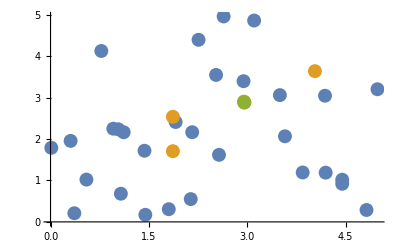

7.65019×10^6

{111,75,164,73}

```mathematica
population = GenerateInitialPopulation[n];

Do[
population = NextPopulation[population];
supplyFromRegionals
,{iteration, 1, 50}
];

maximum = MaximalBy[population, GetProfits][[1]];

ListPlot[{storeLocations[[All,1;;2]], maximum[[2;;-1]],{maximum[[1]]}},PlotStyle->PointSize[.025]]

GetProfits[maximum]

supplyFromRegionals
```